# Hatsuda QNMs Method

Author: Marco Knipfer
Reproducing the paper: 1906.07232, author: Hatsuda

Metric g = -f(r)dt^2+1/(f(r))dr^2+r^2 dΩ^2
f(r) --> differential equation in the form (d^2/(dr_*)^2+ω^2-V(r_*))ϕ =0
Calculate the QNMs for this differential equation using the Hatsuda method.
Only works if the potential V has a maximum.

## Improvements over Hatsuda

- No need to explicitly know the tortoise coordinate
- General potential/metric, dimension

## ToDo

- Not sure if (1-s^2) factor in Vgeneral is correct or only works for my example
- Use for new metrics
- Reproduce Reissner-Nordström
- could be made faster by not requiring the calculation of the Taylor series of the potential every run
- show convergence

## All in One Function

```mathematica
Needs["BenderWu`"]
Clear[QNM]
QNM[{s_,l_,n_, vars_, r0metric_, d_},order_,prec_]:=QNM[{s,l,n, R, r0metric, d},order,prec]=Block[
(*
DESCRIPTION:
-Calculate the QNM of order n with s,l as parameters,
 -vars are general veriables if you use a different potential,
 -r0metric is r0 appearing in the metric and connected to the horizon radius
OUTPUT:
{qnm, poles of Borel transform, rhorizon}	
*)
{$MaxExtraPrecision=2prec,
$MinPrecision=prec,rs,tempOrder,padeOrder,  c, ,f, V, VV, Vgeneral,r0,δsSeries, dfm1, δSeries, δsSeries2,VSeries,v,BW,ϵpert,ϵpertBPT,ϵBPLT,rplus, ω},

BorelTransform[ϵpert_, ℏ_] := ϵpert/.{ℏ^nn_ -> ℏ^nn/nn!};
BorelPadeTransform[ϵpert_, ζ_,Padeorder_]:=PadeApproximant[BorelTransform[ϵpert, ℏ]/.{ℏ->ζζ}, {ζζ, 0, Padeorder}]/.{ζζ->ζ};
LaplaceTrafo[ϵpertBPT_] := NIntegrate[Exp[-t]ϵpertBPT/.ζ->I t,{t,0,∞},WorkingPrecision->prec,MaxRecursion->50];
ω[ϵBPLT_] := Sqrt[-(v[0] + 2 I ϵBPLT)];
PolesTable[ϵpertBPT_] := ζ/.Solve[NumeratorDenominator[ϵpertBPT][[2]]==0, ζ];

c =l(l+d-3);
tempOrder = 2 order + 2;
padeOrder = order/2;

f[r_] :=1 - (r0metric/r)^(d-3) (*+ r^2/R^2*);
Vgeneral[r_, fgeneral_] := ((d-2)(d-4))/(4 r^2)fgeneral[r] + (d-2)/(2r)(1-s^2)fgeneral'[r] + l(l+d-3)/r^2;
V[r_] :=  f[r]Vgeneral[r, f]//Simplify;
r0 = r/.FindRoot[D[V[r],r] == 0, {r, 1.5}, WorkingPrecision->prec];

δsSeries = (Series[1/f[r0+δδ], {δδ, 0, tempOrder}, Assumptions->{δδ∈Reals}]*δδ)/.{δδ->δ};
δsSeries2 =((Normal@ δsSeries)/.{δ^nn_ -> δ^nn / nn})+ O[δ]^(tempOrder+1);
δSeries =Normal@InverseSeries[δsSeries2, δs];
VSeries=Series[-V[r0+δSeries],{δs,0,tempOrder}]//Normal; 

(* V(Subscript[r, 0]+δ(δ_*)) expansion of V in δ_**)
v[k_]:=Coefficient[VSeries,δs,k];
BW=BenderWu[1/2 Sum[v[k] x^k,{k,2,2order+2}],x,n,order];
ϵpert=BWProcess[BW,OutputStyle->"Series",Coupling->Sqrt[ℏ]];
ϵpertBPT = BorelPadeTransform[ϵpert, ζ, padeOrder];ϵBPLT = LaplaceTrafo[ϵpertBPT]; (*Borel-Pade-Laplace-transformed*)
rplus = Module[{froots, realRoots},
froots = Solve[f[r]==0, r];
realRoots=Cases[froots,_?(FreeQ[N[#,16],Complex]&)];
Max[r/.realRoots]
]//N;

{ω[ϵBPLT], PolesTable[ϵpertBPT], rplus, ϵBPLT}
]
```

```mathematica
qnm = QNM[{2,2,1, 0, 1, 4}, 50, 100]; (* prec=100 is too low for order 50 I think *)
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

```mathematica
qnm[[1]]//N (*QNM*)
```

0.693422-0.54783 ⅈ

poles on the positive real axis are bad.

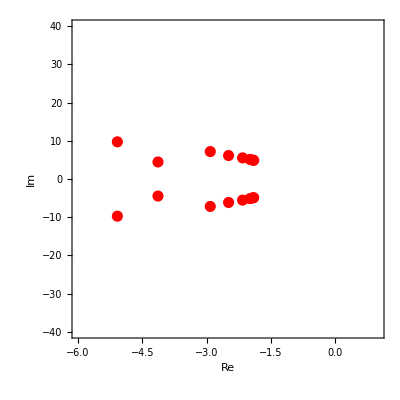

```mathematica
polesTable = qnm[[2]];
ListPlot[{Re[#],Im[#]}&/@(Flatten@polesTable),AxesOrigin->{0,0},ImagePadding->50,AspectRatio->1,Frame->True,FrameLabel->{{Im,None},{Re,"complex plane"}},PlotStyle->Directive[Red,PointSize[.02]],
PlotRange->{{-6, 1},{-40, 40}}]
```

```mathematica
qnm[[3]] (* horizon radius, might not be explicit in the definition of the metric *)
```

1.

# Table on p. 9 Hatsuda

s=2

```mathematica
qnms2 = Table[QNM[{2,l,n, 1, 1, 4}, 50, 100],{l,2,4}, {n,0,2}];
```

N::precsm: Requested precision 16 is smaller than $MinPrecision. Using $MinPrecision instead.

General::stop: Further output of N::precsm will be suppressed during this calculation.

l=2

```mathematica
qnms2[[1,;;,1]]//MatrixForm//N
```

(0.747343-0.177925 ⅈ
0.693422-0.54783 ⅈ
0.602104-0.956552 ⅈ)

l=3

```mathematica
qnms2[[2, ;;,1]]//MatrixForm//N
```

(1.19889-0.185406 ⅈ
1.16529-0.562596 ⅈ
1.10337-0.958186 ⅈ)

l = 4

```mathematica
qnms2[[3, ;;,1]]//MatrixForm//N
```

(1.61836-0.188328 ⅈ
1.59326-0.568669 ⅈ
1.54542-0.959816 ⅈ)